# CINEMÁTICA DIRECTA ROBOT 4GDL 4RSS-ESPACIO.

## FUNCIONES

```mathematica
(*Matriz de Rotación 3x3*)
Rx[α_]:={{1,0,0},{0, Cos[α], -Sin[α]},{0,Sin[α], Cos[α]}}
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0},{-Sin[ϕ],0,Cos[ϕ]}}
Rz[θ_]:={{Cos[θ], -Sin[θ],0},{Sin[θ], Cos[θ],0},{0,0,1}}
(*Matriz de Traslación Homogenea*)
Tx[x_]:={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
Ty[y_]:={{1,0,0,0},{0,1,0,y},{0,0,1,0},{0,0,0,1}}
Tz[z_]:={{1,0,0,0},{0,1,0,0},{0,0,1,z},{0,0,0,1}}
(*Matriz de Rotación Homogenea*)
Qx[α_]:={{1,0,0,0},{0,Cos[α],-Sin[α],0},{0,Sin[α],Cos[α],0},{0,0,0,1}}
Qy[ϕ_]:={{Cos[ϕ],0,Sin[ϕ],0},{0,1,0,0},{-Sin[ϕ],0,Cos[ϕ],0},{0,0,0,1}}
Qz[θ_]:={{Cos[θ],-Sin[θ],0,0},{Sin[θ],Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}
Q[θ_,d_,a_,α_]:=Qz[θ].Tz[d].Tx[a].Qx[α]
(*Vector "n"*)
n={0,0,0,1};
Tm={{nxm,oxm,axm,xm},{nym,oym,aym,ym},{nzm,ozm,azm,zm},{0,0,0,1}};(*Matriz Punto medio *)
T={{nx,ox,ax,x},{ny,oy,ay,y},{nz,oz,az,z},{0,0,0,1}} ;(*matriz resultante*)

T3D[P_]:={P⟦1⟧, P⟦2⟧,P⟦3⟧}
M3D[A_]:={{A⟦1,1⟧,A⟦1,2⟧ , A⟦1,3⟧},{A⟦2,1⟧,A⟦2,2⟧ , A⟦2,3⟧},{A⟦3,1⟧,A⟦3,2⟧ , A⟦3,3⟧}}

(*Función para la evolución de las variables articulares*)
Grafica[tabla_, rojo_,verde_,azul_,EjeX_,EjeY_]:=ListPlot[tabla,ImageSize->300, Joined->True, PlotStyle->{AbsoluteThickness[6], RGBColor[rojo,verde,azul]},BaseStyle->{14,FontFamily->"Arial"}, Frame->True, FrameLabel->{EjeX,EjeY},GridLines->Automatic, PlotRange->All];
```

### Procedimiento para cinemática directa por MTH

MTH1. Enumerar los eslabones comenzando con el primer eslabón móvil de la cadena, al cual se le asigna el número 1, hasta el último eslabón móvil será el valor “N”. Se considera como eslabón Cero a la base fija del robot. 
MTH2. Numerar cada articulación comenzando por la correspondiente al primer GDL, asignándole el número 1 hasta la ultima articulación que será el valor “N“
MTH3. Establecer el sistema  inercial en la base fija del robot, es decir en el eslabón cero, dicho sistema debe de ser dextrógiro  Y por cada eslabón se tendrá un sistema de referencia. 
Las reglas para definir los sistemas de los eslabones móviles son:}
1) Seleccionar ya sea el eje X, o el eje Y, o el eje Z, para ser alineado al eslabón; Por lo regular se selecciona al eje X, y dicho sistema se puede colocar al inicio o al final del eslabón. 
MTH4. Establecer las matrices asociadas a cada eslabón. Se tendrán las matrices ^(i-1)(A_i)
Donde “i” indica el número del sistema. {S_i}
MTH5. Obtener la matriz ^0 A_n=^0 A_1.^1 A_2...^(n-1)A_n
MTH6. Extraer los elementos de posición y de orientación de la matriz ^0 A_n

## Matrices homogéneas de los eslabones.

## MTH4. CIENEMÁTICA DIRECTA

```mathematica
Underoverscript[a, 10, 0]=Underoverscript[a, 11, 0]=Qy[μ11+180°].Tx[ℓ10x].Qz[-60°];
Underoverscript[a, 12, 11]=Qx[θ11].Tx[d12];
Underoverscript[a, 16, 12]=Qz[θ13].Qy[θ14].Qx[θ15].Tx[ℓ13];
θ15=0;
θ14=-θ17;
θ18=180°-θ13;
Underoverscript[a, 110, 16]=Qy[θ17].Qz[θ18].Tx[ℓ14];
```

## DH15. MATRZ HOMEGENA EN EL SISTEMA CERO

```mathematica
Underoverscript[a, 12, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11]//Simplify;
Underoverscript[a, 16, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11].Underoverscript[a, 16, 12]//Simplify;
Underoverscript[a, 110, 0]=Underoverscript[a, 11, 0].Underoverscript[a, 12, 11].Underoverscript[a, 16, 12].Underoverscript[a, 110, 16]//Simplify;

Underoverscript[a, 110, 0]//MatrixForm
```

(Cos[μ11]/2 | 1/2 √3 Cos[θ11] Cos[μ11]+Sin[θ11] Sin[μ11] | 1/2 √3 Cos[μ11] Sin[θ11]-Cos[θ11] Sin[μ11] | -1/2 Cos[μ11] (d12+2 ℓ10x-ℓ14+ℓ13 Cos[θ13] Cos[θ17]+√3 ℓ13 Cos[θ11] Cos[θ17] Sin[θ13]-√3 ℓ13 Sin[θ11] Sin[θ17])-ℓ13 (Cos[θ17] Sin[θ11] Sin[θ13]+Cos[θ11] Sin[θ17]) Sin[μ11]
(√3)/2 | -Cos[θ11]/2 | -Sin[θ11]/2 | 1/2 (-√3 d12+√3 ℓ14-√3 ℓ13 Cos[θ13] Cos[θ17]+ℓ13 Cos[θ11] Cos[θ17] Sin[θ13]-ℓ13 Sin[θ11] Sin[θ17])
-Sin[μ11]/2 | Cos[μ11] Sin[θ11]-1/2 √3 Cos[θ11] Sin[μ11] | -Cos[θ11] Cos[μ11]-1/2 √3 Sin[θ11] Sin[μ11] | 1/2 (-2 ℓ13 Cos[θ11] Cos[μ11] Sin[θ17]+(d12+2 ℓ10x-ℓ14-√3 ℓ13 Sin[θ11] Sin[θ17]) Sin[μ11]+ℓ13 Cos[θ17] (-2 Cos[μ11] Sin[θ11] Sin[θ13]+(Cos[θ13]+√3 Cos[θ11] Sin[θ13]) Sin[μ11]))
0 | 0 | 0 | 1)

## DH16. ELEMENTOS DE POSCIÓN Y DE ORIENTA CIÓN

### VECTOR DE POSICIÓN DEL EFECTOR FINAL

```mathematica
X1=Underoverscript[a, 110, 0]⟦1,4⟧
Y1=Underoverscript[a, 110, 0]⟦2,4⟧
Z1=Underoverscript[a, 110, 0]⟦3,4⟧
```

-1/2 Cos[μ11] (d12+2 ℓ10x-ℓ14+ℓ13 Cos[θ13] Cos[θ17]+√3 ℓ13 Cos[θ11] Cos[θ17] Sin[θ13]-√3 ℓ13 Sin[θ11] Sin[θ17])-ℓ13 (Cos[θ17] Sin[θ11] Sin[θ13]+Cos[θ11] Sin[θ17]) Sin[μ11]

1/2 (-√3 d12+√3 ℓ14-√3 ℓ13 Cos[θ13] Cos[θ17]+ℓ13 Cos[θ11] Cos[θ17] Sin[θ13]-ℓ13 Sin[θ11] Sin[θ17])

1/2 (-2 ℓ13 Cos[θ11] Cos[μ11] Sin[θ17]+(d12+2 ℓ10x-ℓ14-√3 ℓ13 Sin[θ11] Sin[θ17]) Sin[μ11]+ℓ13 Cos[θ17] (-2 Cos[μ11] Sin[θ11] Sin[θ13]+(Cos[θ13]+√3 Cos[θ11] Sin[θ13]) Sin[μ11]))

### MATRIZ DE ROTACIÓN 3X3 ORIENTACIÓN DEL EFECTOR FINAL

```mathematica
Underoverscript[R, 2, 0]=M3D[Underoverscript[a, 2, 0]];
Underoverscript[R, 2, 0]//MatrixForm;

NX=Underoverscript[R, 2, 0]⟦1,1⟧;
OX=Underoverscript[R, 2, 0]⟦1,2⟧;
AX=Underoverscript[R, 2, 0]⟦1,3⟧;

NY=Underoverscript[R, 2, 0]⟦2,1⟧;
OY=Underoverscript[R, 2, 0]⟦2,2⟧;
AY=Underoverscript[R, 2, 0]⟦2,3⟧;

NZ=Underoverscript[R, 2, 0]⟦3,1⟧;
OZ=Underoverscript[R, 2, 0]⟦3,2⟧;
AZ=Underoverscript[R, 2, 0]⟦3,3⟧;
```

## CINEMÁTICA INVERSA POR MÉTODO ALGEBRAICO

```mathematica
ECLDX1= (X1 * -2);
ECLIX1= (x * -2);
ECLDY1= (Y1 * 2) +√3 d12;
ECLIY1= (y * 2) +√3 d12;
ECLDZ1= (Z1 * 2);
ECLIZ1= (z * 2);

EC1= (ECLDY1)^2+(ECLIY1)^2//FullSimplify
solTheta11=Solve[EC1==0,θ11]
```

(√3 ℓ14-√3 ℓ13 Cos[θ13] Cos[θ17]+ℓ13 Cos[θ11] Cos[θ17] Sin[θ13]-ℓ13 Sin[θ11] Sin[θ17])^2+(Cos[μ11] (d12+2 ℓ10x-ℓ14+ℓ13 Cos[θ13] Cos[θ17]+√3 ℓ13 (Cos[θ11] Cos[θ17] Sin[θ13]-Sin[θ11] Sin[θ17]))+2 ℓ13 (Cos[θ17] Sin[θ11] Sin[θ13]+Cos[θ11] Sin[θ17]) Sin[μ11])^2

## θ2

```mathematica
CO2=Solve[EC1==x^2+y^2,Cos[θ2]] //Flatten;
C2=Cos[θ2]/.CO2
S2=√(1-(C2)^2)
t2=ArcTan[C2,S2]
```

Cos[θ2]

√(1-Cos[θ2]^2)

ArcTan[Cos[θ2],√(1-Cos[θ2]^2)]

## θ1

```mathematica
X'=TrigExpand[X];
Y'=TrigExpand[Y];
EC2=Solve[X'==x,Cos[θ1]]//Flatten;
(*EC2=Solve[{X'==x,Y'==y },{Cos[θ1],Sin[θ1]}]//Flatten//Simplify;
C1=Cos[θ1]/.EC2⟦1⟧ ;
S1=Sin[θ1]/.EC2⟦2⟧;*)
C1=Cos[θ1]/.EC2;
Y''=Y'/.Cos[θ1]-> C1;
EC3=Solve[Y''==y,Sin[θ1]]//Flatten;
S1=Sin[θ1]/.EC3 //Simplify
C1'=√(1-(S1)^2)
t1=ArcTan[C1',S1]
```

Sin[θ1]

√(1-Sin[θ1]^2)

ArcTan[√(1-Sin[θ1]^2),Sin[θ1]]

## Trayectoria

```mathematica
(*DATOS*)
ℓ1=40;
ℓ2=30;
af={0,0,-1};
of={1,0,0};
nf=Cross[of,af]
nx=0; ox=1; ax=0;
ny=1; oy=0; ay=0;
nz=0; oz=0; az=-1;
tf=100;  
Cero={0,0,0};
aa=4;

For[t=0, t≤tf, t+=1,
(*ECUACIÓN DE LA RECTA DADO DOS PUNTOS*)
λ=t/tf;
Trayectoria[t]={2*aa*Cos[2*Pi*λ]-aa*Cos[4*Pi*λ]+20,2*aa*Sin[4*Pi*λ]-aa*Sin[4*Pi*λ]+20,0(*2*aa*Cos[2*Pi*λ]-aa*Cos[4*Pi*λ]+0*)};
];

Tablaxyz=Table[{Trayectoria[t]⟦1⟧,Trayectoria[t]⟦2⟧,Trayectoria[t]⟦3⟧}, {t,0,tf,1}];
TrayectoriaEF=Line[Tablaxyz];


Graphics3D[
{
{AbsoluteThickness[1], RGBColor[1,0,0], TrayectoriaEF}
},
Axes->True, AxesLabel->{Ejex, Ejey, EjeZ}, AxesStyle->{Red, Green, Blue},BaseStyle->{14, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-100, 100},{-100, 100},{-60,60}}
]
```

{0,1,0}

-Graphics3D-

## Valores de las Variables Articulares en Cinematica Inversa

```mathematica
For[t=0,t<tf,t+=1,
x=Trayectoria[t]⟦1⟧;
y=Trayectoria[t]⟦2⟧;
z=Trayectoria[t]⟦3⟧;
θ2a[t]=t2;
θ2=θ2a[t];
θ1a[t]=t1;
θ1=θ1a[t];

]
θ1a[10]//N
θ2a[10]//N
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Cos[θ2].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of √(1-Sin[θ1]^2).

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Cos[θ2].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

ArcTan[√(1.-1. Sin[θ1a[1.]]^2),Sin[θ1a[1.]]]

ArcTan[Cos[θ2a[1.]],√(1.-1. Cos[θ2a[1.]]^2)]

## SIMULACIÓN

```mathematica
Animate[
θ1=θ1a[t];
θ2=θ2a[t];

Eslabon1=Line[{Cero,T3D[Underoverscript[a, 1, 0].n]}];
Eslabon2=Line[{T3D[Underoverscript[a, 1, 0].n],T3D[Underoverscript[a, 2, 0].n]}];

Graphics3D[
{
{AbsoluteThickness[1], RGBColor[1,0,0], TrayectoriaEF},
{AbsoluteThickness[6], RGBColor[1,1,0], Eslabon1},
{AbsoluteThickness[5], RGBColor[1,0,1], Eslabon2}

},
Axes->True, AxesLabel->{Ejex, Ejey, EjeZ}, AxesStyle->{Red, Green, Blue},BaseStyle->{14, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-100, 100},{-100, 100},{-100,100}}
], {t,0,tf,1}
]
```

## EVOLUCIÓN DE LAS VARIABLES ARTICULARES

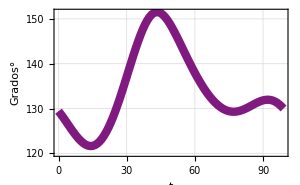

```mathematica
Tabla1=Table[{t, (θ2a[t])/Degree},{t,0,tf,1}];
Theta1=Grafica[Tabla1,.5,.1,.5,"t", "Grados°"]
```

```mathematica
Tabla2=Table[{t, (θ2/.VarArt[t])/Degree},{t,0,tf,1}];
Theta2=Grafica[Tabla2,0,.1,0,"t", "Grados°"]
```

ReplaceAll::reps: {VarArt[0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {VarArt[1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {VarArt[2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {VarArt[0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {VarArt[1.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {VarArt[2.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

(√3 ℓ13 Cos[θ13] Cos[θ17]-ℓ13 Cos[θ11] Cos[θ17] Sin[θ13]+ℓ13 Sin[θ11] Sin[θ17])^2+1/4 (Cos[μ11] (d12+2 ℓ10x-ℓ14+ℓ13 Cos[θ13] Cos[θ17]+√3 ℓ13 (Cos[θ11] Cos[θ17] Sin[θ13]-Sin[θ11] Sin[θ17]))+2 ℓ13 (Cos[θ17] Sin[θ11] Sin[θ13]+Cos[θ11] Sin[θ17]) Sin[μ11])^2

{Sin[θ13]→(2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2-1/2 √3 d12 ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2-√3 ℓ10x ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2+1/2 √3 ℓ13 ℓ14 Cos[θ11] Cos[θ17] Cos[μ11]^2-1/2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2 Cos[μ11]^2+2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17]+3/2 ℓ13^2 Cos[θ11] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]-d12 ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-2 ℓ10x ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13 ℓ14 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-ℓ13^2 Cos[θ13] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]-√3 ℓ13^2 Cos[θ11]^2 Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]+√3 ℓ13^2 Cos[θ17] Cos[μ11] Sin[θ11]^2 Sin[θ17] Sin[μ11]-2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17] Sin[μ11]^2-√((-2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2+1/2 √3 d12 ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2+√3 ℓ10x ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2-1/2 √3 ℓ13 ℓ14 Cos[θ11] Cos[θ17] Cos[μ11]^2+1/2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2 Cos[μ11]^2-2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17]-3/2 ℓ13^2 Cos[θ11] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]+d12 ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+2 ℓ10x ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-ℓ13 ℓ14 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ13] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+√3 ℓ13^2 Cos[θ11]^2 Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]-√3 ℓ13^2 Cos[θ17] Cos[μ11] Sin[θ11]^2 Sin[θ17] Sin[μ11]+2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17] Sin[μ11]^2)^2-4 (ℓ13^2 Cos[θ11]^2 Cos[θ17]^2+3/4 ℓ13^2 Cos[θ11]^2 Cos[θ17]^2 Cos[μ11]^2+√3 ℓ13^2 Cos[θ11] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ17]^2 Sin[θ11]^2 Sin[μ11]^2) (-3 d12^2-x^2-4 √3 d12 y-4 y^2+6 d12 ℓ14+4 √3 y ℓ14-3 ℓ14^2+3 ℓ13^2 Cos[θ13]^2 Cos[θ17]^2+1/4 d12^2 Cos[μ11]^2+d12 ℓ10x Cos[μ11]^2+ℓ10x^2 Cos[μ11]^2-1/2 d12 ℓ14 Cos[μ11]^2-ℓ10x ℓ14 Cos[μ11]^2+1/4 ℓ14^2 Cos[μ11]^2+1/2 d12 ℓ13 Cos[θ13] Cos[θ17] Cos[μ11]^2+ℓ10x ℓ13 Cos[θ13] Cos[θ17] Cos[μ11]^2-1/2 ℓ13 ℓ14 Cos[θ13] Cos[θ17] Cos[μ11]^2+1/4 ℓ13^2 Cos[θ13]^2 Cos[θ17]^2 Cos[μ11]^2+2 √3 ℓ13^2 Cos[θ13] Cos[θ17] Sin[θ11] Sin[θ17]-1/2 √3 d12 ℓ13 Cos[μ11]^2 Sin[θ11] Sin[θ17]-√3 ℓ10x ℓ13 Cos[μ11]^2 Sin[θ11] Sin[θ17]+1/2 √3 ℓ13 ℓ14 Cos[μ11]^2 Sin[θ11] Sin[θ17]-1/2 √3 ℓ13^2 Cos[θ13] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]+ℓ13^2 Sin[θ11]^2 Sin[θ17]^2+3/4 ℓ13^2 Cos[μ11]^2 Sin[θ11]^2 Sin[θ17]^2+d12 ℓ13 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]+2 ℓ10x ℓ13 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]-ℓ13 ℓ14 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]+ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]-√3 ℓ13^2 Cos[θ11] Cos[μ11] Sin[θ11] Sin[θ17]^2 Sin[μ11]+ℓ13^2 Cos[θ11]^2 Sin[θ17]^2 Sin[μ11]^2)))/(2 (ℓ13^2 Cos[θ11]^2 Cos[θ17]^2+3/4 ℓ13^2 Cos[θ11]^2 Cos[θ17]^2 Cos[μ11]^2+√3 ℓ13^2 Cos[θ11] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ17]^2 Sin[θ11]^2 Sin[μ11]^2)),Sin[θ13]→(2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2-1/2 √3 d12 ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2-√3 ℓ10x ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2+1/2 √3 ℓ13 ℓ14 Cos[θ11] Cos[θ17] Cos[μ11]^2-1/2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2 Cos[μ11]^2+2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17]+3/2 ℓ13^2 Cos[θ11] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]-d12 ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-2 ℓ10x ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13 ℓ14 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-ℓ13^2 Cos[θ13] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]-√3 ℓ13^2 Cos[θ11]^2 Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]+√3 ℓ13^2 Cos[θ17] Cos[μ11] Sin[θ11]^2 Sin[θ17] Sin[μ11]-2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17] Sin[μ11]^2+√((-2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2+1/2 √3 d12 ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2+√3 ℓ10x ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2-1/2 √3 ℓ13 ℓ14 Cos[θ11] Cos[θ17] Cos[μ11]^2+1/2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2 Cos[μ11]^2-2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17]-3/2 ℓ13^2 Cos[θ11] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]+d12 ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+2 ℓ10x ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-ℓ13 ℓ14 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ13] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+√3 ℓ13^2 Cos[θ11]^2 Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]-√3 ℓ13^2 Cos[θ17] Cos[μ11] Sin[θ11]^2 Sin[θ17] Sin[μ11]+2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17] Sin[μ11]^2)^2-4 (ℓ13^2 Cos[θ11]^2 Cos[θ17]^2+3/4 ℓ13^2 Cos[θ11]^2 Cos[θ17]^2 Cos[μ11]^2+√3 ℓ13^2 Cos[θ11] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ17]^2 Sin[θ11]^2 Sin[μ11]^2) (-3 d12^2-x^2-4 √3 d12 y-4 y^2+6 d12 ℓ14+4 √3 y ℓ14-3 ℓ14^2+3 ℓ13^2 Cos[θ13]^2 Cos[θ17]^2+1/4 d12^2 Cos[μ11]^2+d12 ℓ10x Cos[μ11]^2+ℓ10x^2 Cos[μ11]^2-1/2 d12 ℓ14 Cos[μ11]^2-ℓ10x ℓ14 Cos[μ11]^2+1/4 ℓ14^2 Cos[μ11]^2+1/2 d12 ℓ13 Cos[θ13] Cos[θ17] Cos[μ11]^2+ℓ10x ℓ13 Cos[θ13] Cos[θ17] Cos[μ11]^2-1/2 ℓ13 ℓ14 Cos[θ13] Cos[θ17] Cos[μ11]^2+1/4 ℓ13^2 Cos[θ13]^2 Cos[θ17]^2 Cos[μ11]^2+2 √3 ℓ13^2 Cos[θ13] Cos[θ17] Sin[θ11] Sin[θ17]-1/2 √3 d12 ℓ13 Cos[μ11]^2 Sin[θ11] Sin[θ17]-√3 ℓ10x ℓ13 Cos[μ11]^2 Sin[θ11] Sin[θ17]+1/2 √3 ℓ13 ℓ14 Cos[μ11]^2 Sin[θ11] Sin[θ17]-1/2 √3 ℓ13^2 Cos[θ13] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]+ℓ13^2 Sin[θ11]^2 Sin[θ17]^2+3/4 ℓ13^2 Cos[μ11]^2 Sin[θ11]^2 Sin[θ17]^2+d12 ℓ13 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]+2 ℓ10x ℓ13 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]-ℓ13 ℓ14 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]+ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]-√3 ℓ13^2 Cos[θ11] Cos[μ11] Sin[θ11] Sin[θ17]^2 Sin[μ11]+ℓ13^2 Cos[θ11]^2 Sin[θ17]^2 Sin[μ11]^2)))/(2 (ℓ13^2 Cos[θ11]^2 Cos[θ17]^2+3/4 ℓ13^2 Cos[θ11]^2 Cos[θ17]^2 Cos[μ11]^2+√3 ℓ13^2 Cos[θ11] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ17]^2 Sin[θ11]^2 Sin[μ11]^2))}

(2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2-1/2 √3 d12 ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2-√3 ℓ10x ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2+1/2 √3 ℓ13 ℓ14 Cos[θ11] Cos[θ17] Cos[μ11]^2-1/2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2 Cos[μ11]^2+2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17]+3/2 ℓ13^2 Cos[θ11] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]-d12 ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-2 ℓ10x ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13 ℓ14 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-ℓ13^2 Cos[θ13] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]-√3 ℓ13^2 Cos[θ11]^2 Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]+√3 ℓ13^2 Cos[θ17] Cos[μ11] Sin[θ11]^2 Sin[θ17] Sin[μ11]-2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17] Sin[μ11]^2-√((-2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2+1/2 √3 d12 ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2+√3 ℓ10x ℓ13 Cos[θ11] Cos[θ17] Cos[μ11]^2-1/2 √3 ℓ13 ℓ14 Cos[θ11] Cos[θ17] Cos[μ11]^2+1/2 √3 ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17]^2 Cos[μ11]^2-2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17]-3/2 ℓ13^2 Cos[θ11] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]+d12 ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+2 ℓ10x ℓ13 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]-ℓ13 ℓ14 Cos[θ17] Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ13] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+√3 ℓ13^2 Cos[θ11]^2 Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]-√3 ℓ13^2 Cos[θ17] Cos[μ11] Sin[θ11]^2 Sin[θ17] Sin[μ11]+2 ℓ13^2 Cos[θ11] Cos[θ17] Sin[θ11] Sin[θ17] Sin[μ11]^2)^2-4 (ℓ13^2 Cos[θ11]^2 Cos[θ17]^2+3/4 ℓ13^2 Cos[θ11]^2 Cos[θ17]^2 Cos[μ11]^2+√3 ℓ13^2 Cos[θ11] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ17]^2 Sin[θ11]^2 Sin[μ11]^2) (-3 d12^2-x^2-4 √3 d12 y-4 y^2+6 d12 ℓ14+4 √3 y ℓ14-3 ℓ14^2+3 ℓ13^2 Cos[θ13]^2 Cos[θ17]^2+1/4 d12^2 Cos[μ11]^2+d12 ℓ10x Cos[μ11]^2+ℓ10x^2 Cos[μ11]^2-1/2 d12 ℓ14 Cos[μ11]^2-ℓ10x ℓ14 Cos[μ11]^2+1/4 ℓ14^2 Cos[μ11]^2+1/2 d12 ℓ13 Cos[θ13] Cos[θ17] Cos[μ11]^2+ℓ10x ℓ13 Cos[θ13] Cos[θ17] Cos[μ11]^2-1/2 ℓ13 ℓ14 Cos[θ13] Cos[θ17] Cos[μ11]^2+1/4 ℓ13^2 Cos[θ13]^2 Cos[θ17]^2 Cos[μ11]^2+2 √3 ℓ13^2 Cos[θ13] Cos[θ17] Sin[θ11] Sin[θ17]-1/2 √3 d12 ℓ13 Cos[μ11]^2 Sin[θ11] Sin[θ17]-√3 ℓ10x ℓ13 Cos[μ11]^2 Sin[θ11] Sin[θ17]+1/2 √3 ℓ13 ℓ14 Cos[μ11]^2 Sin[θ11] Sin[θ17]-1/2 √3 ℓ13^2 Cos[θ13] Cos[θ17] Cos[μ11]^2 Sin[θ11] Sin[θ17]+ℓ13^2 Sin[θ11]^2 Sin[θ17]^2+3/4 ℓ13^2 Cos[μ11]^2 Sin[θ11]^2 Sin[θ17]^2+d12 ℓ13 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]+2 ℓ10x ℓ13 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]-ℓ13 ℓ14 Cos[θ11] Cos[μ11] Sin[θ17] Sin[μ11]+ℓ13^2 Cos[θ11] Cos[θ13] Cos[θ17] Cos[μ11] Sin[θ17] Sin[μ11]-√3 ℓ13^2 Cos[θ11] Cos[μ11] Sin[θ11] Sin[θ17]^2 Sin[μ11]+ℓ13^2 Cos[θ11]^2 Sin[θ17]^2 Sin[μ11]^2)))/(2 (ℓ13^2 Cos[θ11]^2 Cos[θ17]^2+3/4 ℓ13^2 Cos[θ11]^2 Cos[θ17]^2 Cos[μ11]^2+√3 ℓ13^2 Cos[θ11] Cos[θ17]^2 Cos[μ11] Sin[θ11] Sin[μ11]+ℓ13^2 Cos[θ17]^2 Sin[θ11]^2 Sin[μ11]^2))